SUS304
Q^-1vsL

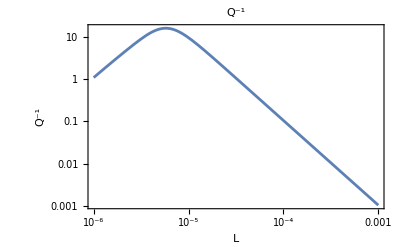

```mathematica
QwoHeatFlow =δE Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ]/.
{δE->32,ξ->6.4 10^-6/L};
QHeatFlowg=LogLogPlot[QwoHeatFlow,{L,0.000001,0.001},PlotLabel->"Q^-1", Frame->True,FrameLabel->{L,"Q^-1"}]
```

```mathematica
QHeatFlow=δE Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.{δE->32,ξ->6.4 10^-6/L}; (*sapphire*)
```

d=1.1,1.3,1.7

9.15527×10^16 Abs[(L^3 (-(0.0000128 (Cos[0.00001344/L] Cosh[(6.4×10^-7)/L]+Cos[(6.4×10^-7)/L] Cosh[0.00001344/L]))/L-Cosh[0.00001344/L] Sin[(6.4×10^-7)/L]+Cosh[(6.4×10^-7)/L] Sin[0.00001344/L]-Cos[0.00001344/L] Sinh[(6.4×10^-7)/L]+Cos[(6.4×10^-7)/L] Sinh[0.00001344/L]))/(Cos[0.00001408/L]+Cosh[0.00001408/L])]

9.15527×10^16 Abs[(L^3 (-(0.0000128 (Cos[0.00001472/L] Cosh[(1.92×10^-6)/L]+Cos[(1.92×10^-6)/L] Cosh[0.00001472/L]))/L-Cosh[0.00001472/L] Sin[(1.92×10^-6)/L]+Cosh[(1.92×10^-6)/L] Sin[0.00001472/L]-Cos[0.00001472/L] Sinh[(1.92×10^-6)/L]+Cos[(1.92×10^-6)/L] Sinh[0.00001472/L]))/(Cos[0.00001664/L]+Cosh[0.00001664/L])]

9.15527×10^16 Abs[(L^3 (-(0.0000128 (Cos[0.00001728/L] Cosh[(4.48×10^-6)/L]+Cos[(4.48×10^-6)/L] Cosh[0.00001728/L]))/L-Cosh[0.00001728/L] Sin[(4.48×10^-6)/L]+Cosh[(4.48×10^-6)/L] Sin[0.00001728/L]-Cos[0.00001728/L] Sinh[(4.48×10^-6)/L]+Cos[(4.48×10^-6)/L] Sinh[0.00001728/L]))/(Cos[0.00002176/L]+Cosh[0.00002176/L])]

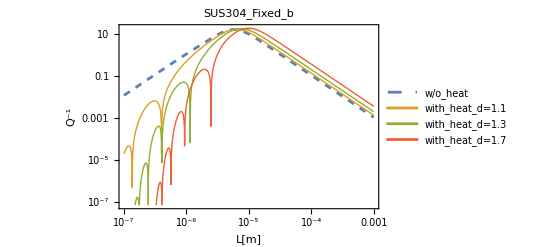

```mathematica
Q11=QHeatFlow/.{d->1.1}
Q13=QHeatFlow/.{d->1.3}
Q17=QHeatFlow/.{d->1.7}
HeatFlowg=LogLogPlot[{QwoHeatFlow,Q11,Q13,Q17},{L,0.0000001,0.001},PlotLabel->"SUS304_Fixed_b", Frame->True,FrameLabel->{"L[m]","Q^-1"},PlotLegends->Placed[{"w/o_heat","with_heat_d=1.1","with_heat_d=1.3","with_heat_d=1.7"},{0.7,0.25}],GridLinesStyle->LightGray,GridLines->Full,PlotStyle->{Dashed,Thick,Thick,Thick}]
```